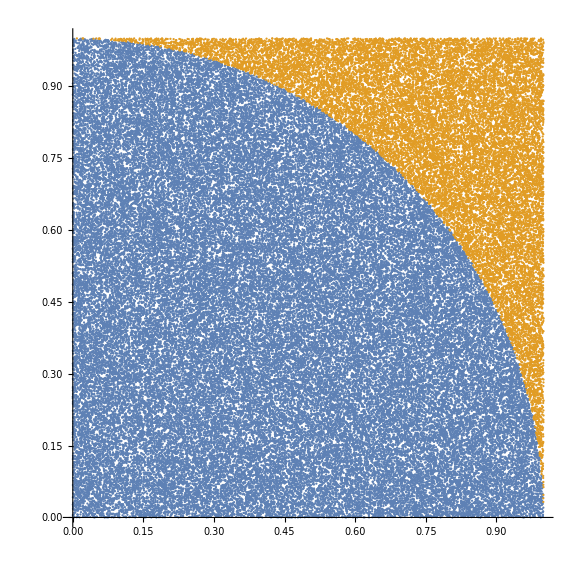

```mathematica
SetOptions[ListPlot,AspectRatio->1,ImageSize->Large];
ListPlot@GatherBy[RandomReal[{0,1},{100000,2}],√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&]
```

```mathematica
Manipulate[Module[{all,points,insides,outsides},
all = RandomReal[{0,1},{n,2}];
points=GatherBy[all,√((#_⟦1⟧)^2+(#_⟦2⟧)^2)<1&];
{insides,outsides} = points;
ListPlot[points, PlotLabel->Style[4(Length@insides)/(Length@all)//N,30],AspectRatio->1,ImageSize->Large]],{n,100,100000,100},TrackedSymbols:> {n},ContinuousAction->False]
```

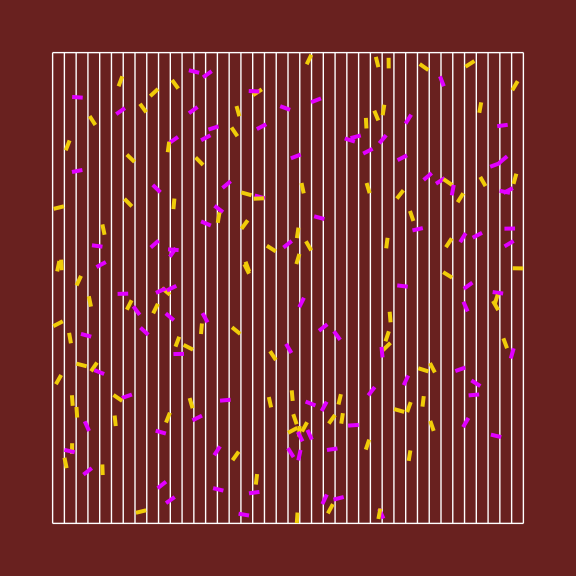

```mathematica
Module[{L,d,l,n,yellow,brown,pink,knit,buffonNeedles,verticalLines,horizontalLines,grid},
L=40;
d=1;
l = d-0.1;
n=200;
yellow = RGBColor[0.941176, 0.8, 0.0352941];
brown = RGBColor[0.411765, 0.129412, 0.121569];
pink=RGBColor[0.882353, 0, 1];
knit[{x_,y_,angle_}]:=Style[
Line[{{x -l/2 Cos@angle,y -l/2 Sin@angle},{x +l/2 Cos@angle,y +l/2 Sin@angle }}],
If[x -l/2 Cos@angle≤Round[x] d ≤x +l/2 Cos@angle,pink,yellow],
Thickness[0.005]];
buffonNeedles =knit/@MapThread[{#1_⟦1⟧,#1_⟦2⟧,#2}&,{RandomReal[{0+l/2,L-l/2},{n,2}],RandomReal[{-π/2,π/2},n]}];
verticalLines = Table[Line[{{x d,0},{x d,L d}}],{x,0,L d,d}];
horizontalLines = Line@#&/@{List[{0,0},{L d,0}],List[{0,L d},{L d,L d}]};
grid = Style[#,White]&/@Join[verticalLines,horizontalLines];
Graphics[Join[grid,buffonNeedles],AspectRatio->1,Background->brown,ImageSize->Large]]
```

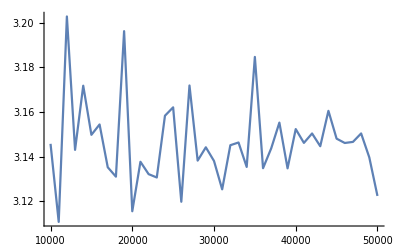

```mathematica
Module[{L=200,d=1,l,knit,buffonNeedles},ListLinePlot[Table[
l = d-0.1;
knit[{x_,angle_}]:={x -l/2 Cos@angle,x,x +l/2 Cos@angle};
buffonNeedles =knit/@MapThread[{#1,#2}&,{RandomReal[{0+l/2,L-l/2},n],RandomReal[{-π/2,π/2},n]}];
{n,(2l Length@buffonNeedles)/(Length@Select[buffonNeedles,#_⟦1⟧≤ Round[#_⟦2⟧]d≤#_⟦3⟧&]d)},{n,10000,50000,1000}],PlotRange->Full]]
```